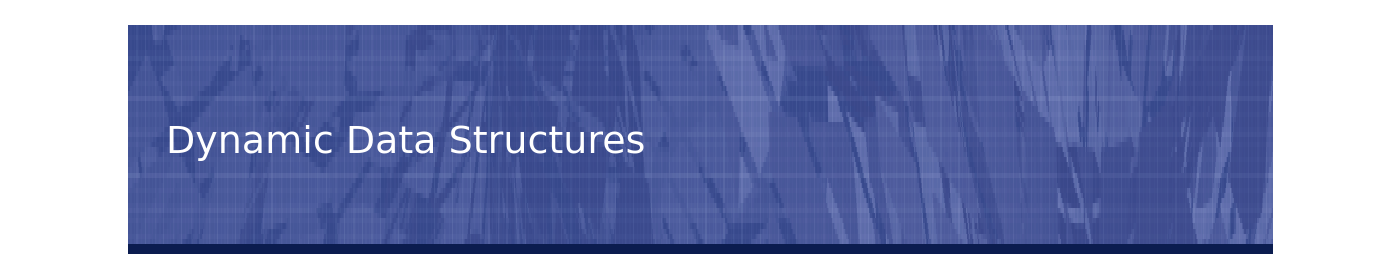
# 

## Presenter

Valeriu Ungureanu

## Data

DayName, Day MonthName Year

## Moldova State University

Normative Course

### Хеш-таблицы Hash Tables

Для многих приложений достаточны динамические множества, поддерживающие только стандартные словарные операции: вставки, поиска и удаления.

Хеш-таблица - ассоциативный массив для хранения пар ключей и их значений, в котором ключ может быть представлен в виде хеш-функции.

Напомним, что ассоциативный массив называемый также  таблицей (associative array, map, symbol table, or dictionary) представляет собой набор элементов каждый из которых организован в виде пары <K, V>, где K — ключ, а V — значение  элемента (его тело или информационная часть), при этом каждый возможный ключ появляется максимум один раз в наборе.

В языке Wolfram это:

Association[]

Примером ассоциативного массива (таблицы) может служить телефонный  справочник: значением в данном случае является совокупность «Ф. И. О. + адрес», а ключом — номер телефона, один номер телефона имеет одного владельца, но один человек может иметь несколько номеров.

Реализация ассоциативных массивов (таблиц) ставит проблему словаря, классическую проблему информатики: задачу разработки структуры данных, которая поддерживает набор данных во время операций «поиска», «удаления» и «вставки».

Два основных решения проблемы словаря - это хеш-таблица и дерево поиска. В некоторых случаях также возможно решить проблему, используя массивы с прямой адресацией, бинарные деревья поиска или другие более специализированные структуры.

-Graphics-

Операции вставки, поиска и удаления выполняются в среднем за время О(1).

В худшем случае поиск выполняется за время О(n).

Хеш-таблица представляет собой обобщение обычного массива. Напомним, что возможность прямой индексации элементов обычного массива обеспечивает доступ к произвольной позиции в массиве за время O(1).

Если количество реально хранящихся в массиве ключей мало по сравнению с количеством возможных значений ключей, эффективной альтернативой массива с прямой индексацией становится хеш-таблица, которая обычно использует массив с размером, пропорциональным количеству реально хранящихся в нем ключей. Вместо непосредственного использования ключа в качестве индекса массива, индекс вычисляется по значению ключа.

Хеширование представляет собой исключительно эффективную и практичную технологию — в среднем все базовые словарные операции требуют только O (1) времени.

### Таблицы с прямой адресацией Direct-adress tables

#### Таблицы с прямой адресацией

Прямая адресация хорошо работает для небольших множеств ключей, которые  характеризуются тем что каждый их элемент имеет ключ из пространтства ключей

U = {0, 1, . . . , m − 1},

где m не слишком велико. При этом, никакие два элемента не имеют одинаковых ключей.

Для представления динамического множества используется массив, или таблица с прямой адресацией T [0..m − 1], каждая позиция, или ячейка (position, slot), которой соответствует ключу из U.

-Graphics-

Ячейка k указывает на элемент множества с ключом k.

Если множество не содержит элемента с ключом k, то T [k] = NIL.

Каждый ключ из пространства U = {0, 1, . . . , 9} соответствует индексу таблицы.

Множество реальных ключей K = {2, 3, 5, 8} определяет ячейки таблицы, которые содержат указатели на элементы. Остальные ячейки содержат значение NIL.

Реализация словарных операций тривиальна:

DIRECT_ADDRESS_SEARCH(T, k)
return T[k]

DIRECT_ADDRESS_INSERT(T, x)
T[key[x]] ← x

DIRECT_ADDRESS_DELETE(T, x)
T[key[x]] ← NIL

Каждая из приведенных операций очень быстрая: время их работы равно O (1).

В некоторых приложениях элементы динамического множества могут храниться непосредственно в таблице с прямой адресацией - вместо хранения ключей и сопутствующих данных элементов в объектах, внешних по отношению к таблице с прямой адресацией. 

Зачастую хранение ключа не является необходимым условием поскольку если известен индекс объекта в таблице, тем самым знаком  и его ключ.  Однако, если ключ не хранится в ячейке таблицы то нужен какой-то иной механизм для того что-бы помечать пустые ячейки.

### Хеш таблицы Hash tables

to hash - мелко порубить, перемешать

#### Кратко о хеш таблицах

Недостаток прямой адресации очевиден: если пространство ключей U велико, хранение таблицы T размером |U| непрактично, а то и вовсе невозможно — в зависимости от количества доступной памяти и размера пространства ключей.

Кроме того множество K реально сохраненных ключей может быть мало по сравнению с пространством ключей U, а в этом случае память выделенная для таблицы T, в основном расходуется напрасно.

-Graphics-

Когда множество K хранящихся в словаре ключей гораздо меньше пространства возможных ключей U, хеш-таблица требует существенно меньше места, чем таблица с прямой адресацией. Требования к памяти могут быть снижены до Θ(|K|), при этом время поиска элемента в хеш-таблице остается равным O (1).

В случае прямой адресации элемент с ключом k хранится в ячейке k. При хешировании этот элемент хранится в ячейке h (k), т.е. мы используем хеш-функцию h для вычисления ячейки для данного ключа k.

Функция h отображает пространство ключей U на ячейки хеш-таблицы T[0..m − 1]:

h : U → {0, 1, . . . , m −1} .

Говорят в таком случае, что элемент с ключом k хешируется в ячейку h (k);
величина h (k) называется хеш-значением ключа k.

-Graphics-

Цель хеш-функции состоит в том, чтобы уменьшить рабочий диапазон индексов массива, и вместо |U| значений использовать лишь m значений. Соответственно, снижаются требования к количеству памяти.

В этом контексте возникает одна проблема: два ключа могут быть хешированы в одну и ту же ячейку. Такая ситуация называется коллизией.

Имеются эффективные технологии для разрешения конфликтов, вызываемых коллизиями. 

Идеальным решением было бы полное устранение коллизий, но полностью избежать коллизий невозможно в принципе. Хорошая хеш-функция в состоянии только минимизировать количество коллизий.

Одной из идей решения выделенной проблемы заключается в том, чтобы сделать h "случайной".

C другой стороны, h должна быть  детерминистической в смысле того что для одного и того-же значения k всегда давать одно и то же хеш-значение h (k).

Но, поскольку |U| >> m, как минимум два ключа имеют одинаковое хеш-значение. Таким образом, полностью избежать коллизий невозможно в принципе, и хорошая хеш-функция в состоянии только минимизировать количество коллизий. Таким образом, нам крайне необходим метод разрешения возникающих коллизий.

#### Разрешение коллизий при помощи цепочек

При использовании данного метода все элементы, хешированные в одну и ту же ячейку, объединяются в связанный список.

-Graphics-

Ячейка j содержит указатель на заголовок списка всех элементов, хеш-значение ключа которых равно j; если таких элементов нет, ячейка содержит значение NIL. На выше-приведенном рисунке показано разрешение коллизий, возникающих из-за того, что

h (k_1) = h (k_4),
h (k_2) = h (k_5) = h (k_7),
h (k_6) = h (k_8).

Словарные операции в хеш-таблице с использованием цепочек для разрешения коллизий реализуются очень просто:

CHAINED_HASH_INSERT(T, x)
	Вставить x в заголовок списка T[h(key[x])]

CHAINED_HASH_SEARCH(T, k)
	Поиск элемента с ключом k в списке T[h(k)]

CHAINED_HASH_DELETE(T, x)
	Удаление x из списка T[h(key[x])]

Время, необходимое для вставки в наихудшем случае, равно O (1). Процедура вставки выполняется очень быстро, поскольку предполагается, что вставляемый элемент отсутствует в таблице. При необходимости это предположение может быть проверено путем выполнения поиска перед вставкой.

Время работы поиска в наихудшем случае пропорционально длине списка. Удаление элемента может быть выполнено за время O (1) при использовании двусвязных списков.

#### Анализ хеширования с цепочками

Насколько высока производительность хеширования с цепочками? В частности, сколько времени требуется для поиска элемента с данным ключом?

Пусть T хеш-таблица с m ячейками, в которых хранятся n элементов.

Определим коэффициент заполнения таблицы T как α=n/m, т.е. как среднее количество элементов, хранящихся в одной цепочке.

Значение величины α может быть меньше, равна или больше единицы.

В наихудшем случае хеширование с цепочками ведет себя крайне неприятно: все n ключей хешированы в одну и ту же ячейку, создавая список длиной n. Т. о., время поиска в наихудшем случае равно Θ(n) плюс время вычисления хеш-функции, что ничуть не лучше чем в случае использования связанного списка для хранения всех n элементов. Понятно что использование хеш-таблиц в наихудшем случае совершенно бессмысленно.

Средняя производительность хеширования зависит от того насколько хорошо хеш-функция h распределяет множество сохраняемых ключей по m ячейкам в среднем. Будем полагать что все элементы хешируются по ячейкам равномерно и независимо и назовем данное предположение “простым равномерным хешированием” (simple uniform hashing).

Обозначим длины списков T [j] для j = 0, 1, . . . , m − 1 как n_j, так что

n=n_0+n_1+...+n_(m-1),

а среднее значение n_j равно E[n_j]=α=n/m.

Считаем, что хеш-значение h (k) может быть вычислено за время O (1), так что время, необходимое для поиска элемента с ключом k, линейно зависит от длины n_(h(k)) списка T [h (k)].

Не учитывая время O (1), требующееся для вычисления хеш-функции и доступа к ячейке h (k), рассмотрим математическое ожидание количества элементов, которое должно быть проверено алгоритмом поиска (т.е. количество элементов в списке T [h (k)], которые проверяются на равенство их ключей величине k).

Должны быть рассмотрены два случая:

1. поиск неудачен и в таблице нет элементов с ключом k,

2. поиск заканчивается успешно и в таблице определяется элемент с ключом k.

Теорема 1. В хеш-таблице с разрешением коллизий методом цепочек математическое ожидание времени неудачного поиска в предположении простого равномерного хеширования равно Θ(1+α).

Доказательство. В предположении простого равномерного хеширования любой ключ k, который еще не находится в таблице, может быть помещен с равной вероятностью в любую из m ячеек. Математическое ожидание времени неудачного поиска ключа k равно времени поиска до конца списка T [h (k)], математическое ожидание длины которого E[n_(h(k))]=α. Таким образом, при неудачном поиске математическое ожидание количества проверяемых элементов равно α, а общее время, необходимое для поиска, включая время вычисления хеш-функции h (k), равно Θ(1+α).  □

Успешный поиск несколько отличается от неудачного, поскольку вероятность поиска в списке различна для разных списков и пропорциональна количеству содержащихся в нем элементов. Тем не менее, и в этом случае математическое ожидание времени поиска остается равным Θ(1+α).

Теорема 2. В хеш-таблице с разрешением коллизий методом цепочек математическое ожидание времени успешного поиска в предположении простого равномерного хеширования в среднем равно Θ(1+α).

Доказательство. Мы считаем, что искомый элемент с равной вероятностью может быть любым элементом, хранящимся в таблице. Количество элементов, проверяемых в процессе успешного поиска элемента x, на 1 больше, чем количество элементов, находящихся в списке перед x. Элементы, находящиеся в списке до x, были вставлены в список после того, как элемент x был сохранен в таблице, так как новые элементы помещаются в начало списка. Для того чтобы найти математическое ожидание количества проверяемых элементов, мы возьмем среднее значение по всем элементам таблицы, которое равно 1 плюс математическое ожидание количества элементов, добавленных в список после искомого.

Пусть x_i обозначает i-й элемент, вставленный в таблицу (i = 1, 2, . . . , n), а k_i = key [x_i]. Определим для ключей k_i и k_j индикаторную случайную величину X_ij=I{h(k_i)=h(k_j)}. В предположении простого равномерного хеширования, Pr{h(k_i)=h(k_j)}=1/m и, в соответствии с известной леммой,  E[X_ij]=1/m. Таким образом, математическое ожидание числа проверяемых элементов в случае успешного поиска равно

E[1/n∑_(i=1)^n (1+∑_(j=i+1)^n X_ij)]=
=1/n∑_(i=1)^n (1+∑_(j=i+1)^n E[X_ij])=
=1/n∑_(i=1)^n (1+∑_(j=i+1)^n 1/m)=
=1+1/nm∑_(i=1)^n (n-i)=
 =1+1/nm(∑_(i=1)^n n-∑_(i=1)^n i)=
1+1/nm(n^2-(n(n+1))/2)=
=1+(n-1)/m=
=1+α/2-α/(2n).

Следовательно, полное время, необходимое для проведения успешного поиска (включая время на вычисление хеш-функции), составляет Θ(2+α/2-α/(2n))=Θ(1+α).  □

Что же означает проведенный анализ? Если количество ячеек в хеш-таблице, как минимум, пропорционально количеству элементов, хранящихся в ней, то n = O (m) и, следовательно,

α = n/m = O (m)/m = O (1),

означающее что поиск элемента в хеш-таблице в среднем требует постоянного времени. Поскольку в худшем случае вставка элемента в хеш-таблицу занимает O (1) времени (как и удаление элемента при использовании двусвязных списков), можно сделать вывод, что все словарные операции в хеш-таблице в среднем выполняются за время O (1).

### Хеш-функции Hash functions

Рассмотрим три схемы построения хеш-функций:

1) хеширование делением и 2) хеширование умножением, эвристичные по своей природе,

и 3) универсальное хеширование — использующее рандомизацию для обеспечения доказуемого качества.

#### Чем определяется качество хеш-функции?

Качественная хеш-функция удовлетворяет предположению простого равномерного хеширования:

для каждого ключа равновероятно помещение в любую из m ячеек, независимо от хеширования остальных ключей.

Это условие обычно невозможно проверить, поскольку, как правило, распределение вероятностей, в соответствии с которым поступают вносимые в таблицу ключи, неизвестно; кроме того, вставляемые ключи могут не быть независимыми.

Иногда распределение вероятностей оказывается известным. Например, если известно, что ключи представляют собой случайные действительные числа, равномерно распределенные в диапазоне 0 ≤ k < 1, то хеш-функция h (k) = ⌊k m⌋ удовлетворяет условию простого равномерного хеширования.

На практике при построении качественных хеш-функций зачастую используются различные эвристические методики. В процессе построения большую помощь оказывает информация о распределении ключей.

При построении хеш-функции хорошим подходом является подбор функции таким образом, чтобы она никак не коррелировала с закономерностями, которым могут подчиняться существующие данные.

Например, метод деления, вычисляет хеш-значение как остаток от деления ключа на некоторое простое число. Если это простое число никак не связано с распределением исходных данных, метод часто дает хорошие результаты.

Некоторые приложения хеш-функций могут накладывать дополнительные требования, помимо требований простого равномерного хеширования.

Например, можно потребовать, чтобы "близкие" в некотором смысле ключи давали далекие хеш-значения. Универсальное хеширование, зачастую приводит к желаемым результатам.

#### Ключи как целые неотрицательные числа

Для большинства хеш-функций пространство ключей представляется множеством целых неотрицательных чисел N = {0, 1, 2, . . .}. Если же ключи не являются целыми неотрицательными числами, то можно найти способ их интерпретации как таковых. 

Например, строка символов может рассматриваться как целое число, записанное в соответствующей системе счисления. Так, идентификатор pt можно рассматривать как пару десятичных чисел (112, 116), поскольку в ASCII-наборе символов p = 112 и t = 116. Рассматривая pt как число в системе счисления с основанием 128, оно соответствует значению 112 ・ 128 + 116 = 14452.

В конкретных приложениях обычно не представляет особого труда разработать метод для представления ключей в виде (возможно, больших) целых чисел.

Далее все ключи расматриваются как целые неотрицательные числа.

#### Метод деления

Построение хеш-функции методом деления состоит в отображении ключа k в одну из ячеек путем получения остатка от деления k на m:

h (k) = k mod m.

Например, если хеш-таблица имеет размер m = 12, а значение ключа k = 100, то h (k) = 4. 
Поскольку для вычисления хеш-функции требуется только одна операция деления, хеширование методом деления считается достаточно быстрым.

При использовании данного метода обычно избегают некоторых значения m. 
Например, m не должно быть степенью 2, поскольку если m = 2^P, то h (k) представляет собой просто p младших битов числа k. Если только заранее не известно, что все наборы младших p битов ключей равновероятны, лучше строить хеш-функцию таким образом, чтобы ее результат зависел от всех битов ключа.

Зачастую хорошие результаты можно получить, выбирая в качестве значения m простое число, достаточно далекое от степени двойки.

Предположим, например, что мы хотим создать хеш-таблицу с разрешением коллизий методом цепочек для хранения n = 2000 символьных строк, размер символов в которых равен 8 битам. Нас устраивает проверка в среднем трех элементов при неудачном поиске, так что мы выбираем размер таблицы равным m = 701.

Число 701 выбрано как простое число, близкое к 2000/3 и не являющееся степенью 2.
Рассматривая каждый ключ k как целое число, получается искомая хеш-функция:

```mathematica
m=701;
h[k_]:=Mod[k,m]
```

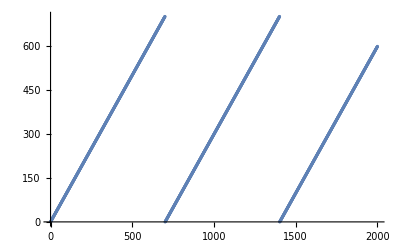

```mathematica
ListPlot[h/@Range[2000]]
```

#### Метод умножения

Построение хеш-функции методом умножения выполняется в два этапа. Сначала мы умножаем ключ k на константу 0 < A < 1 и получаем дробную часть полученного произведения. Затем мы умножаем полученное значение на m и применяем к нему функцию “пол” т.е.

h (k) = ⌊m {kA} ⌋,

где {kA}  = kA −⌊kA⌋ - дробная часть произведения kA.

Достоинство метода умножения заключается в том, что значение m перестает быть критичным. Обычно величина m из соображений удобства реализации функции выбирается равной степени 2. Пусть у нас имеется компьютер с размером слова w битов и k помещается в одно слово. Ограничим возможные значения константы A видом s/2^w, где s — целое число из диапазона 0 < s < 2^w. Тогда мы сначала умножаем k на w-битовое целое число s = A 2^w. Результат представляет собой 2w-битовое число r_1 2^w+r_0, где r_1 — старшее слово произведения а r_0  — младшее. Старшие p битов числа r_0 представляют собой искомое p-битовое хеш-значение.

-Graphics-

Хотя описанный метод работает с любыми значениями константы A, некоторые значения дают лучшие результаты по сравнению с другими. Оптимальный выбор зависит от характеристик хешируемых данных. Кнут предложил использовать дающее неплохие результаты значение

A ≈(√5-1)/2≈ 0.6180339887 . . .

Возьмем в качестве примера:

```mathematica
k=123456;p=14;m=2^14;w=32;
```

Принимая предложение Кнута, выбираем значение A в виде s/2^w, ближайшее к величине (√5-1)/2, так что A = 2654435769/2^32.

```mathematica
Maximize[{s/2^32-(√5-1)/2,s/2^32-(√5-1)/2≤0},{s,Integers}]
```

{1/2 (1-√5)+1/2 (-1+√5),{s→2147483648 (-1+√5),ℤ→0}}

```mathematica
s=Floor[2147483648 (-1+√5)]
```

2654435769

Тогда k ・ s = 327 706 022 297 664 = (76 300 ・ 2^32).02+ 17 612 864,

```mathematica
IntegerDigits[k s,2^32]
```

{76300,17612864}

и соответственно r_1=76300 и r_0=17612864. Старшие 14 битов числа r_0

```mathematica
Length@IntegerDigits[17612864,2]
```

25

```mathematica
FromDigits[Join[{0,0,0,0,0,0,0},IntegerDigits[17612864,2]][[1;;14]],2]
```

67

```mathematica
Length@IntegerDigits[k s,2^32]
```

2

дают нам хеш значение h (k) = 67.

```mathematica
h[k_]:=With[{l=IntegerDigits[IntegerDigits[2654435769k,2^32]⟦2⟧ ,2]},FromDigits[Join[ConstantArray[0,32-Length@l],l]⟦1;;14⟧,2]]
```

```mathematica
h[123456]
```

67

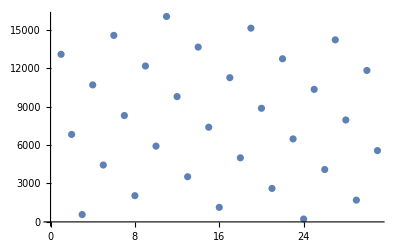

```mathematica
ListPlot[h/@Range[9970,10000]]
```

#### Универсальное хеширование

Если недоброжелатель будет умышленно выбирать ключи для хеширования при помощи конкретной хеш-функции, то он сможет подобрать n значений, которые будут хешироваться в одну и ту же ячейку таблицы, приводя к среднему времени выборки Θ(n). Такимобразом любая фиксированная хеш-функция становится уязвимой и единственный эффективный выход из ситуации— случайный выбор хеш-функции не зависящий от того с какими именно ключами ей предстоит работать Такой подход который называется универсальным хешированием, гарантирует хорошую производительность в среднем независимо от того какие данные будут выбраны злоумышленником.

Главная идея универсального хеширования состоит в случайном выборе хеш-функции из некоторого тщательно отобранного класса функций в начале работы программы. Как и в случае быстрой сортировки, рандомизация гарантирует, что одни и те же входные данные не могут постоянно давать наихудшее поведение алгоритма. В силу рандомизации алгоритм будет работать всякий раз по-разному, даже для одних и тех же входных данных, что гарантирует высокую среднюю производительность для любых входных данных. Возвращаясь к примеру с таблицей символов компилятора, мы обнаружим, что никакой выбор программистом имен идентификаторов не может привести к постоянному снижению производительности хеширования. Такое снижение возможно только тогда, когда компилятором выбрана случайная хеш-функция, которая приводит к плохому хешированию конкретных входных данных; однако вероятность такой ситуации очень мала и одинакова для любого множества идентификаторов одного и то же размера.

Пусть H — конечное множество хеш-функций которые отображают пространствоключей U в диапазон {0, 1, 2, . . . , m −1}. Такое множество называется универсальным, если для каждой пары различных ключей k, l ∈ U количество хеш-функций h∈H, для которых h (k) = h (l), непревышает |H|/m. Другими словами, при случайном выборе хеш-функции из H вероятность коллизии между различными ключами k и l не превышает вероятности совпадения двух случайным образом выбранных хеш-значений из множества {0, 1, 2, . . . , m −1}, которая равна 1/m.

Построить универсальное множество хеш-функций довольно просто, что следует из теории чисел. Начнем с выбора простого числа p, достаточно большого, чтобы все возможные ключи находились в диапазоне от 0 до p−1 включительно. Пусть:

Z_p = {0, 1, . . . , p − 1},
Z_p^* = {1, 2, . . . , p −1}.

Поскольку p — простое число, существуют методы решения уравнения по модулю p. Из предположения о том что пространство ключей больше чем количество ячеек в хеш-таблице, следует что p > m.

Теперь определим хеш-функцию h_(a,b) для любых a ∈ Z_p^* и b ∈ Z_p следующим образом:

h_(a,b)(k)= ((ak + b) mod p) mod m. 		(*)

Например при p = 17 и m = 6 h_(3,4)(8)=5. Семейство всех таких функций образует множество:

H_(p,m)(k)= {h_(a,b): a∈Z_p^*и b∈Z_p}.		(**)

Каждая хеш-функция h_(a,b) отображает  Z_p на Z_m. Этот класс хеш-функций обладает тем свойством что размер m выходного диапазона произволен и не обязательно представляет собой простое число. Поскольку число a можно выбрать p −1 способом, a число b можно выбрать p способами, всего во множестве H_(p,m) содержится p (p −1) хеш-функций.

Теорема 3. Множество хеш-функций H_(p,m), определяемое уравнениями (*) и (**), является универсальным.

### Открытая адресация Open addressing

При открытой адресации все элементы хранятся непосредственно в хеш-таблице, т.е. каждая запись таблицы содержит либо элемент динамического множества, либо значение NIL.

При поиске элемента систематически проверяются ячейки таблицы до тех пор, пока не найден искомый элемент или пока не определено его отсутствие в таблице.

В отличие от метода цепочек, нет ни списков, ни элементов, хранящихся вне таблицы.

В методе открытой адресации хеш-таблица может оказаться заполненной, делая невозможной вставку новых элементов; коэффициент заполнения α не может превышать 1.

Конечно, при хешировании с разрешением коллизий методом цепочек можно использовать свободные места в хеш-таблице для хранения связанных списков , но преимущество открытой адресации заключается в том, что она позволяет полностью отказаться от указателей.

Вместо того чтобы следовать по указателям, вычисляется последовательность проверяемых ячеек. Дополнительная память, освобождающаяся в результате отказа от указателей, позволяет использовать хеш-таблицы большего размера при том-же общем количестве памяти потенциально приводя к меньшему количеству коллизий и более быстрой выборке.

Для выполнения вставки при открытой адресации последовательно проверяются или исследуются   ячейки хеш-таблицы до тех пор пока не найдена пустая ячейка в которую помещается вставляемый ключ. Вместо фиксированного порядка исследования ячеек 0, 1, . . . , m −1 (для чего требуется Θ(n) времени), последовательность исследуемых ячеек зависит от вставляемого в таблицу ключа. Для определения исследуемых ячеек хеш-функция расширяется включением в нее вкачестве второго аргумента номера исследования. В результате хеш-функция становится следующей

h : U × {0, 1, . . . , m − 1} → {0, 1, . . . , m −1} .

В методе открытой адресации требуется, чтобы для каждого ключа k последовательность исследований

{h (k, 0) , h (k, 1) , . . . , h (k,m− 1)}.

представляла собой перестановку множества {0, 1, . . . , m − 1}, чтобы в конечном счете могли быть просмотрены все ячейки хеш-таблицы. В приведенном далее псевдокоде предполагается, что элементы в таблице T представляют собой ключи без сопутствующей информации; ключ k тождественен элементу, содержащему ключ k. Каждая ячейка содержит либо ключ, либо значение NIL (если она не заполнена):

HASH_INSERT(T, k)
1 i ← 0
2 repeat j ← h(k, i)
3 	if T[j] = NIL
4 		then T[j] ← k
5 			return j
6 		else i ← i + 1
7 until i = m
8 error “Хеш-таблица переполнена”

Алгоритм поиска ключа k исследует ту же последовательность ячеек, что и алгоритм вставки ключа k. Таким образом, если при поиске встречается пустая ячейка, поиск завершается неуспешно, поскольку ключ k должен был бы быть вставлен в эту ячейку в последовательности исследований, и никак не позже нее. (Мы предполагаем, что удалений из хеш-таблицы не было.) Процедура HASH_SEARCH получает в качестве входных параметров хеш-таблицу T и ключ k и возвращает номер ячейки, которая содержит ключ k (или значение NIL, если ключ в хеш-таблице не обнаружен):

HASH_SEARCH(T, k)
1 i ← 0
2 repeat j ← h(k, i)
3 	if T[j] = k
4 		then return j
5 	i ← i + 1
6 until T[j] = NIL или i = m
7 return NIL

Процедура удаления из хеш-таблицы с открытой адресацией достаточно сложна. При удалении ключа из ячейки i мы не можем просто пометить ее значением NIL. Поступив так, мы можем сделать невозможным выборку ключа k, в процессе вставки которого исследовалась и оказалась занятой ячейка i. Одно из решений состоит в том, чтобы помечать такие ячейки специальным значением DELETED вместо NIL. При этом мы должны слегка изменить процедуру HASH_INSERT, с тем чтобы она рассматривала такую ячейку как пустую и могла вставить в нее новый ключ. В процедуре HASH_SEARCH никакие изменения не требуются, поскольку мы просто пропускаем такие ячейки при поиске и исследуем следующие ячейки в последовательности. Однако при использовании специального значения DELETED время поиска перестает зависеть от коэффициента заполнения α, и по этой причине, как правило, при необходимости удалений из хеш-таблицы в качестве метода разрешения коллизий выбирается метод цепочек.

В нашем дальнейшем анализе мы будем исходить из предположения равномерного хеширования, т.е. мы предполагаем, что для каждого ключа в качестве последовательности исследований равновероятны все m! перестановок множества {0, 1, . . . , m − 1}. Равномерное хеширование представляет собой обобщение определенного ранее простого равномерного хеширования, заключающееся в том, что теперь хеш-функция дает не одно значение, а целую последовательность исследований. Реализация истинно равномерного хеширования достаточно трудна, однако на практике используются подходящие аппроксимации.

Для вычисления последовательности исследований для открытой адресации обычно используются три метода: линейное, квадратичное и двойное хеширование.

Эти методы гарантируют, что для каждого ключа k последовательность исследований {h (k, 0) , h (k, 1) , . . . , h (k,m− 1)} является перестановкой {0, 1, . . . , m − 1}. Однако эти методы не удовлетворяют предположению о равномерном хешировании, так как ни один из них не в состоянии сгенерировать более m^2 различных последовательностей исследований (вместо m!, требующихся для равномерного хеширования). Наибольшее количество последовательностей исследований дает двойное хеширование и, как и следовало ожидать, дает наилучшие результаты.

#### Линейное исследование

Пусть задана обычная хеш-функция

h' : U → {0, 1, . . . , m −1},

называемая вспомогательной хеш-функцией (auxiliary hash function). Метод линейного исследования для вычисления последовательности исследований использует хеш-функцию:

h (k, i) = (h' (k) + i) mod m,

где i принимает значения от 0 до m−1, включительно. Для данного ключа k первой исследуемой ячейкой является T [h’(k)], т.е. ячейка, которую дает вспомогательная хеш-функция.

Далее мы исследуем ячейку T[h’(k) + 1] и далее последовательно все до ячейки T [m − 1], после чего переходим в начало таблицы и последовательно исследуем ячейки T [0], T [1], и так до ячейки T [h’(k) − 1]. Поскольку начальная исследуемая ячейка однозначно определяет всю последовательность исследований целиком, всего имеется m различных последовательностей.

Линейное исследование легко реализуется, однако с ним связана проблема первичной кластеризации, связанной с созданием длинных последовательностей занятых ячеек, что, само собой разумеется, увеличивает среднее время поиска. Кластеры возникают в связи с тем, что вероятность заполнения пустой ячейки, которой предшествуют i заполненных ячеек, равна (i+1)/m. Таким образом, длинные серии заполненных ячеек имеют тенденцию ко все большему удлинению, что приводит к увеличению среднего времени поиска.

#### Квадратичное исследование

Квадратичное исследование использует хеш-функцию вида:

h(k,i)=(h'(k)+c_1 i+c_2 i^2)mod m,

где h’ — вспомогательная хеш-функция, c1 и c2 ≠ 0 — вспомогательные константы а i принимает значения от 0 до m −1, включительно. Начальная исследуемая ячейка — T [h’(k)]; остальные исследуемые позиции смещены относительно нее на величины которые описываются квадратичной зависимостью от номера исследования i. Этот метод работает существенно лучше линейного исследования, но для того чтобы исследование охватывало все ячейки, необходим выбор специальных значений c_1, c_2 и m. Кроме того, если два ключа имеют одну и то женачальную позицию исследования то одинаковы и последовательности исследования в целом, так как из h_1(k,0)=h_2(k,0) вытекает h_1(k,0)=h_2(k,0). Это свойство приводит к более мягкой вторичной кластеризации. Как и в случае линейного исследования начальная ячейка определяет всю последовательность, поэтому всего используется m различных последовательностей исследования.

#### Двойное хеширование

Двойное хеширование представляет собой один из наилучших способов использования открытой адресации, поскольку получаемые при этом перестановки
обладают многими характеристиками случайно выбираемых перестановок. Двойное хеширование использует хеш-функцию вида

h (k, i) =(h_1(k) + i h_2(k)) mod m,

где h_1 и h_2 — вспомогательные хеш-функции. Начальное исследование выполняется в позиции T [h_1(k)], а смещение каждой из последующих исследуемых ячеек относительно предыдущей равно h_2(k) по модулю m. Следовательно, в отличие от линейного и квадратичного исследования в данном случае последовательность исследования зависит от ключа k по двум параметрам — в плане выбора начальной исследуемой ячейки и расстояния между соседними исследуемыми ячейками, так как оба эти параметра зависят от значения ключа.

#### Анализ хеширования с открытой адресацией

Анализ открытой адресации, как и анализ метода цепочек, выполняется с использованием коэффициента заполнения α = n/m хеш-таблицы при n и m, стремящихся к бесконечности. Само собой разумеется, при использовании открытой адресации у нас может быть не более одного элемента на ячейку таблицы, так что n ≤ m и, следовательно, α ≤ 1.

Будем считать, что используется равномерное хеширование. При такой идеализированной схеме последовательность исследований {h(k, 0), h(k, 1), . . . , h(k,
m − 1)}, используемая для вставки или поиска каждого ключа k, с равной вероятностью является одной из возможных перестановок {0, 1, . . . , m − 1}. Разумеется,
с каждым конкретным ключом связана единственная фиксированная последовательность исследований, так что при рассмотрении распределения вероятностей
ключей и хеш-функций все последовательности исследований оказываются равновероятными.

Теорема 4. Математическое ожидание количества исследований при неуспешном поиске в хеш-таблице с открытой адресацией и коэффициентом заполнения α = n/m < 1 в предположении равномерного хеширования не превышает 1/(1 − α).

Теорема 5. Математическое ожидание количества исследований при удачном поиске в хеш-таблице с открытой адресацией и коэффициентом заполнения α < 1, в предположении равномерного хеширования и равновероятного поиска любогоиз ключей, не превышает

1/α ln 1/(1-α)